```mathematica
k≥((c-n)/n);
c>n;
(c-n(k-1))(k+2)+∑_(j=2)^(k+1) n j
```

(2+k) (c-(-1+k) n)+1/2 (3 k n+k^2 n)

```mathematica
FullSimplify[1/n(2+((c-n)/n)) (c-(-1+((c-n)/n)) n)+1/2 (3 ((c-n)/n) n+((c-n)/n)^2 n)]
```

```mathematica
lbps[c_,n_]:=(c^2-2 (-2+n) n+c (4+n))/(2 n)
```

```mathematica
cprime[x_]:=c-∑_(j=1)^(x-1) (n-j)
```

```mathematica
FullSimplify[lbps[c,n]n+(c-n((c-n)/n))lbps[cprime[(c-n)/n+2],(c-n)/n+3]+∑_(j=2)^(((c-n)/n)+1) n*lbps[cprime[j],j+1]]
```

(3 c^5+4 c^4 n (5+2 n)-4 c n^4 (5+2 n) (-1+102 n)+c^3 n^2 (61+16 (4-9 n) n)-96 n^5 (1+2 n (7+2 n))-8 c^2 n^3 (-20+n (73+75 n))+48 n^4 (c+2 n) (1+c+2 n) (5+c+2 n) HarmonicNumber[(c+n)/n])/(96 n^3 (c+2 n))

```mathematica
FullSimplify[%/(c)]
```

(3 c^5+4 c^4 n (5+2 n)-4 c n^4 (5+2 n) (-1+102 n)+c^3 n^2 (61+16 (4-9 n) n)-96 n^5 (1+2 n (7+2 n))-8 c^2 n^3 (-20+n (73+75 n))+48 n^4 (c+2 n) (1+c+2 n) (5+c+2 n) HarmonicNumber[(c+n)/n])/(96 c n^3 (c+2 n))

```mathematica
h≤(3(c+n))/(4n)
```

```mathematica
(h)≥(n 3(c+n))/(4n c)
```

```mathematica
Table[N[HarmonicNumber[(c+n)/n](4n c)/(3(c+n))-n],{n,3,53},{c,n,n+80-1}]
```

```mathematica
Reduce[{n>3,
c>n,
ps≥(3 c^5+4 c^4 n (5+2 n)-4 c n^4 (5+2 n) (-1+102 n)+c^3 n^2 (61+16 (4-9 n) n)-96 n^5 (1+2 n (7+2 n))-8 c^2 n^3 (-20+n (73+75 n))+48 n^4 (c+2 n) (1+c+2 n) (5+c+2 n) (n 3(c+n))/(4n c))/(96 c n^3 (c+2 n)),
ps≤n-2},Integers]
```

(c|n|ps)∈Integers&&((n==4&&5≤c≤70&&(34504704+7532544 c-1611776 c^2-440320 c^3-22576 c^4+208 c^5+3 c^6)/(49152 c^2+6144 c^3)≤ps≤2)||(n==5&&6≤c≤111&&(185625000+33637500 c-5475000 c^2-1297500 c^3-57975 c^4+300 c^5+3 c^6)/(120000 c^2+12000 c^3)≤ps≤3)||(n==6&&7≤c≤161&&(742390272+115426944 c-14981760 c^2-3148416 c^3-123948 c^4+408 c^5+3 c^6)/(248832 c^2+20736 c^3)≤ps≤4)||(n==7&&8≤c≤221&&(2414157480+329349972 c-35285096 c^2-6677524 c^3-234367 c^4+532 c^5+3 c^6)/(460992 c^2+32928 c^3)≤ps≤5)||(n==8&&9≤c≤291&&(6738149376+819855360 c-74416128 c^2-12828672 c^3-405696 c^4+672 c^5+3 c^6)/(786432 c^2+49152 c^3)≤ps≤6)||(n==9&&10≤c≤371&&(16721259624+1837368684 c-144184536 c^2-22846860 c^3-656991 c^4+828 c^5+3 c^6)/(1259712 c^2+69984 c^3)≤ps≤7)||(n==10&&11≤c≤460&&(37800000000+3788400000 c-261200000 c^2-38320000 c^3-1009900 c^4+1000 c^5+3 c^6)/(1920000 c^2+96000 c^3)≤ps≤8)||(n==11&&12≤c≤559&&(79210035432+7299475524 c-448014600 c^2-61220676 c^3-1488663 c^4+1188 c^5+3 c^6)/(2811072 c^2+127776 c^3)≤ps≤9)||(n==12&&13≤c≤667&&(155868364800+13296586752 c-734386176 c^2-93947904 c^3-2120112 c^4+1392 c^5+3 c^6)/(3981312 c^2+165888 c^3)≤ps≤10)||(n==13&&14≤c≤785&&(290882817576+23101850460 c-1158662648 c^2-139368892 c^3-2933671 c^4+1612 c^5+3 c^6)/(5483712 c^2+210912 c^3)≤ps≤11)||(n==14&&15≤c≤912&&(518815148544+38549073024 c-1769287296 c^2-200860800 c^3-3961356 c^4+1848 c^5+3 c^6)/(7375872 c^2+263424 c^3)≤ps≤12)||(n==15&&16≤c≤1050&&(889835625000+62119912500 c-2626425000 c^2-282352500 c^3-5237775 c^4+2100 c^5+3 c^6)/(9720000 c^2+324000 c^3)≤ps≤13)||(n==16&&17≤c≤1196&&(1474918612992+97102331904 c-3803709440 c^2-388366336 c^3-6800128 c^4+2368 c^5+3 c^6)/(12582912 c^2+393216 c^3)≤ps≤14)||(n≥17&&((n<c<Root[360 n^6+864 n^7+288 n^8+(444 n^5+384 n^6+336 n^7) #1+(584 n^4-1144 n^5-168 n^6) #1^2+(352 n^3-464 n^4-348 n^5) #1^3+(61 n^2+64 n^3-108 n^4) #1^4+(20 n+8 n^2) #1^5+3 #1^6&,4]&&(3 c^6+20 c^5 n+61 c^4 n^2+8 c^5 n^2+160 c^3 n^3+64 c^4 n^3+200 c^2 n^4-368 c^3 n^4-108 c^4 n^4+444 c n^5-952 c^2 n^5-348 c^3 n^5+360 n^6+384 c n^6-168 c^2 n^6+864 n^7+336 c n^7+288 n^8)/(96 c^3 n^3+192 c^2 n^4)≤ps≤-2+n)||(c==Root[360 n^6+864 n^7+288 n^8+(444 n^5+384 n^6+336 n^7) #1+(584 n^4-1144 n^5-168 n^6) #1^2+(352 n^3-464 n^4-348 n^5) #1^3+(61 n^2+64 n^3-108 n^4) #1^4+(20 n+8 n^2) #1^5+3 #1^6&,4]&&ps==-2+n))))

```mathematica
Reduce[{n>3,
n(n-3)/2≥c>n,
n-2≥(3 c^5+4 c^4 n (5+2 n)-4 c n^4 (5+2 n) (-1+102 n)+c^3 n^2 (61+16 (4-9 n) n)-96 n^5 (1+2 n (7+2 n))-8 c^2 n^3 (-20+n (73+75 n))+48 n^4 (c+2 n) (1+c+2 n) (5+c+2 n) (n 3(c+n))/(4n c))/(96 c n^3 (c+2 n))},Integers]
```

(c|n)∈Integers&&((n==6&&(c==7||c==8||c==9))||(n≥7&&n<c≤1/2 (-3 n+n^2)))

```mathematica
Reduce[{n>3,n<c≤n(n-3)/2,n-2≥1/n(2+((c-n)/n)) (c-(-1+((c-n)/n)) n)+1/2 (3 ((c-n)/n) n+((c-n)/n)^2 n)},Integers]
```

(c|n)∈Integers&&n≥7&&n<c≤1/2 (-4-n)+1/2 √(16-24 n+17 n^2)

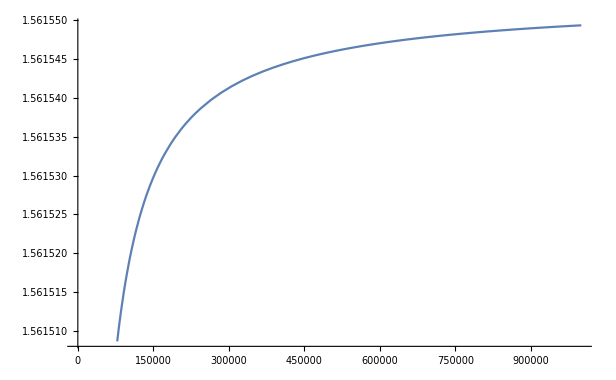

```mathematica
Plot[(1/2 (-4-n)+1/2 √(16-24 n+17 n^2))/n,{n,3,1000000}]
```

```mathematica
Limit[(1/2 (-4-n)+1/2 √(16-24 n+17 n^2))/n,n->∞]
```

1/2 (-1+√17)

```mathematica
N[%]
```

1.56155

```mathematica
Reduce[{
0≤si≤i,
1≤i≤m-1,
0≤s≤m,
si≤s,
m≥2,
x==si^2+si(2+m-s-i)+(1+m-i-s)},x,Integers]
```

(C[1]|C[2]|C[3]|C[4]|C[5])∈Integers&&C[1]≥0&&C[2]≥0&&C[3]≥0&&C[4]≥0&&C[5]≥0&&((i==1+C[1]+C[2]+C[3]&&m==2+C[1]+C[2]+C[3]+C[4]+C[5]&&s==2+C[1]+C[2]+C[4]&&si==1+C[2])||(i==1+C[1]+C[2]+C[3]&&m==2+C[1]+C[2]+C[3]+C[4]+C[5]&&s==1+C[1]+C[2]+C[4]&&si==1+C[2])||(i==1+C[1]+C[2]+C[3]&&m==2+C[1]+C[2]+C[3]+C[4]+C[5]&&s==2+C[1]+C[2]+C[4]&&si==C[2])||(i==1+C[1]+C[2]+C[3]&&m==2+C[1]+C[2]+C[3]+C[4]+C[5]&&s==1+C[1]+C[2]+C[4]&&si==C[2])||(i==1+C[1]+C[2]+C[3]&&m==2+C[1]+C[2]+C[3]+C[4]+C[5]&&s==C[1]+C[2]+C[4]&&si==C[2]))&&x==1-i+m-s+2 si-i si+m si-s si+si^2

```mathematica
LogicalExpand[%]
```

((C[1]|C[2]|C[3]|C[4]|C[5])∈Integers&&x==1-i+m-s+2 si-i si+m si-s si+si^2&&C[2]==si&&1+C[1]+C[2]+C[3]==i&&C[1]+C[2]+C[4]==s&&2+C[1]+C[2]+C[3]+C[4]+C[5]==m&&C[1]≥0&&C[2]≥0&&C[3]≥0&&C[4]≥0&&C[5]≥0)||((C[1]|C[2]|C[3]|C[4]|C[5])∈Integers&&x==1-i+m-s+2 si-i si+m si-s si+si^2&&C[2]==si&&1+C[1]+C[2]+C[3]==i&&1+C[1]+C[2]+C[4]==s&&2+C[1]+C[2]+C[3]+C[4]+C[5]==m&&C[1]≥0&&C[2]≥0&&C[3]≥0&&C[4]≥0&&C[5]≥0)||((C[1]|C[2]|C[3]|C[4]|C[5])∈Integers&&x==1-i+m-s+2 si-i si+m si-s si+si^2&&C[2]==si&&1+C[1]+C[2]+C[3]==i&&2+C[1]+C[2]+C[4]==s&&2+C[1]+C[2]+C[3]+C[4]+C[5]==m&&C[1]≥0&&C[2]≥0&&C[3]≥0&&C[4]≥0&&C[5]≥0)||((C[1]|C[2]|C[3]|C[4]|C[5])∈Integers&&x==1-i+m-s+2 si-i si+m si-s si+si^2&&1+C[2]==si&&1+C[1]+C[2]+C[3]==i&&1+C[1]+C[2]+C[4]==s&&2+C[1]+C[2]+C[3]+C[4]+C[5]==m&&C[1]≥0&&C[2]≥0&&C[3]≥0&&C[4]≥0&&C[5]≥0)||((C[1]|C[2]|C[3]|C[4]|C[5])∈Integers&&x==1-i+m-s+2 si-i si+m si-s si+si^2&&1+C[2]==si&&1+C[1]+C[2]+C[3]==i&&2+C[1]+C[2]+C[4]==s&&2+C[1]+C[2]+C[3]+C[4]+C[5]==m&&C[1]≥0&&C[2]≥0&&C[3]≥0&&C[4]≥0&&C[5]≥0)

```mathematica
Maximize[{si^2+si(2+m-s-i)+(1+m-i-s),0≤si≤i&&1≤i≤m-1&& 0≤s≤m&&si≤s&&m≥2&&Element[si|m|s|i,Integers]},{i}]
```

Maximize[{1-i+m-s+(2-i+m-s) si+si^2,0≤si≤i&&1≤i≤-1+m&&0≤s≤m&&si≤s&&m≥2&&(si|m|s|i)∈Integers},{i}]

```mathematica
ithsum[v_,i_]:=∑_(j=1)^i v[[i]]
```

```mathematica
domax[f_,from_,to_]:=Block[{max=0,thisval=0},
Do[thisval=f[i];If[thisval>max,max=thisval,0],{i,from,to}];max]
```

```mathematica
domax[1-#^2&,-3,5]
```

1

```mathematica
fanmax[t_,m_]:=
Block[{vec=PadLeft[IntegerDigits[t,2],m]},
Block[{total=Total[vec],
sums=Table[ithsum[vec,i],{i,1,m-1}]},
Block[{zsmax=domax[(sums[[#]])^2+(sums[[#]])*(2+m-total-#)+(1+m-#-total)&,1,m-1]},
Max[m+1-total,1+total,zsmax]]]]
```

```mathematica
Timing[Min[Table[fanmax[j,2],{j,0,2^2-1}]]]
```

{0.000212,2}

```mathematica
Timing[Min[Table[fanmax[j,3],{j,0,2^3-1}]]]
```

{0.000554,3}

```mathematica
Timing[Min[Table[fanmax[j,4],{j,0,2^4-1}]]]
```

{0.000903,4}

```mathematica
Timing[Min[Table[fanmax[j,5],{j,0,2^5-1}]]]
```

{0.002153,5}

```mathematica
Timing[Min[Table[fanmax[j,6],{j,0,2^6-1}]]]
```

{0.005262,6}

```mathematica
Timing[Min[Table[fanmax[j,7],{j,0,2^7-1}]]]
```

{0.016032,7}

```mathematica
Timing[Min[Table[fanmax[j,8],{j,0,2^8-1}]]]
```

{0.031697,8}

```mathematica
Timing[Min[Table[fanmax[j,9],{j,0,2^9-1}]]]
```

{0.056134,9}

```mathematica
Timing[Min[Table[fanmax[j,10],{j,0,2^10-1}]]]
```

{0.138458,10}

```mathematica
Timing[Min[Table[fanmax[j,11],{j,0,2^11-1}]]]
```

{0.290848,11}

```mathematica
Timing[Min[Table[fanmax[j,12],{j,0,2^12-1}]]]
```

{0.667794,12}

```mathematica
Timing[Min[Table[fanmax[j,13],{j,0,2^13-1}]]]
```

{1.45868,13}

```mathematica
Timing[Min[Table[fanmax[j,14],{j,0,2^14-1}]]]
```

{3.13277,14}

```mathematica
Timing[Min[Table[fanmax[j,15],{j,0,2^15-1}]]]
```

{6.74034,15}

```mathematica
Timing[Min[Table[fanmax[j,16],{j,0,2^16-1}]]]
```

{14.5506,16}

```mathematica
ParallelDoMin[f_,from_,to_]:=ParallelTable[
```

```mathematica
Table[Mod[2^i,6],{i,1,10}]
```

{2,4,2,4,2,4,2,4,2,4}

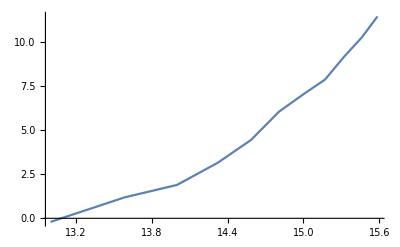

```mathematica
ListPlot[Map[Log2[2^12 Reverse[#]]&,{{0.000212,2},
{0.000554,3},
{0.000903,4},
{0.002153,5},
{0.005262,6},
{0.016032,7},
{0.031697,8},
{0.056134,9},
{0.138458,10},
{0.290848,11},
{0.667794,12}}],Joined->True]
```

```mathematica
fansum[t_,m_]:=
Block[{vec=PadLeft[IntegerDigits[t,2],m]},
Block[{total=Total[vec],
sums=Table[ithsum[vec,i],{i,1,m-1}]},
Block[{zssum=Sum[(sums[[#]])^2+(sums[[#]])*(2+m-total-#)+(1+m-#-total)&[k],{k,1,m-1}]},
Total[{m+1-total,1+total,zssum}]]]]
```

```mathematica
Timing[Min[Table[fansum[j,2],{j,0,2^2-1}]]]
```

{0.000231,5}

```mathematica
Timing[Min[Table[fansum[j,3],{j,0,2^3-1}]]]
```

{0.000377,8}

```mathematica
Timing[Min[Table[fansum[j,4],{j,0,2^4-1}]]]
```

{0.001074,12}

```mathematica
Timing[Min[Table[fansum[j,5],{j,0,2^5-1}]]]
```

{0.001795,17}

```mathematica
Timing[Min[Table[fansum[j,6],{j,0,2^6-1}]]]
```

{0.005106,23}

```mathematica
Timing[Min[Table[fansum[j,7],{j,0,2^7-1}]]]
```

{0.01017,30}

```mathematica
Timing[Min[Table[fansum[j,8],{j,0,2^8-1}]]]
```

{0.023308,38}

```mathematica
Timing[Min[Table[fansum[j,9],{j,0,2^9-1}]]]
```

{0.055479,47}

```mathematica
Timing[Min[Table[fansum[j,10],{j,0,2^10-1}]]]
```

{0.129629,57}

```mathematica
Timing[Min[Table[fansum[j,11],{j,0,2^11-1}]]]
```

{0.259977,68}

```mathematica
Timing[Min[Table[fansum[j,12],{j,0,2^12-1}]]]
```

{0.545559,80}

```mathematica
Timing[Min[Table[fansum[j,13],{j,0,2^13-1}]]]
```

{1.28153,93}

```mathematica
Timing[Min[Table[fansum[j,14],{j,0,2^14-1}]]]
```

{2.78051,107}

```mathematica
Timing[Min[Table[fansum[j,15],{j,0,2^15-1}]]]
```

{5.78344,122}

```mathematica
Timing[Min[Table[fansum[j,16],{j,0,2^16-1}]]]
```

{12.6137,138}

```mathematica
Timing[Min[Table[fansum[j,17],{j,0,2^17-1}]]]
```

{27.4279,155}

```mathematica
Timing[Min[Table[fansum[j,18],{j,0,2^18-1}]]]
```

{58.2863,173}

```mathematica
Timing[Min[Table[fansum[j,19],{j,0,2^19-1}]]]
```

{128.924,192}

```mathematica
Table[{i+1,Map[Last,{{0.000231,5},
{0.000377,8},
{0.001074,12},
{0.001795,17},
{0.005106,23},
{0.01017,30},
{0.023308,38},
{0.055479,47},
{0.129629,57},
{0.259977,68},
{0.545559,80},
{1.281529,93},
{2.780506,107},
{5.783439,122},
{12.613711,138},
{27.427922,155},
{58.28634,173},
{128.924409,192}}][[i]]},{i,1,17}]
```

{{2,5},{3,8},{4,12},{5,17},{6,23},{7,30},{8,38},{9,47},{10,57},{11,68},{12,80},{13,93},{14,107},{15,122},{16,138},{17,155},{18,173}}

```mathematica
InterpolatingPolynomial[%,m]
```

5+(3+1/2 (-3+m)) (-2+m)

```mathematica
Expand[%]
```

2+m/2+m^2/2

```mathematica
FullSimplify[%]
```

1/2 (4+m+m^2)

```mathematica
Reduce[{m(1-e)+e+f(2+m-e)≤0,
m≥2,
0≤e≤m-1,
e<f≤m(m-1)/2},e,Integers]
```

(f|m|e)∈Integers&&m≥6&&((3/2+1/2 √(9+4 m)<f≤-1+m&&(2 f+m+f m)/(-1+f+m)≤e<f)||(-1+m<f<1/3 (1-3 m+m^2)&&(2 f+m+f m)/(-1+f+m)≤e≤-1+m)||(f==1/3 (1-3 m+m^2)&&e==(m+2/3 (1-3 m+m^2)+1/3 m (1-3 m+m^2))/(-1+m+1/3 (1-3 m+m^2))))

```mathematica
Reduce[{(2+m)f-1≤e(m-1)+e f,
(e==0&&f==0)||(e==1&&f≥1)||(e>1&&f>e),
0≤e≤m,
m≥2},Integers]
```

(e|f|m)∈Integers&&((m==2&&e==0&&f==0)||(m≥3&&((e==0&&f==0)||(1/2 (3+√5)<e≤m&&e<f≤(-1+e-e m)/(-2+e-m)))))

```mathematica
ExpandNumerator[1/2 (6+m (3+m))]
```

1/2 (6+3 m+m^2)

```mathematica
∑_(j=1)^m j^2
```

1/6 m (1+m) (1+2 m)

```mathematica
FullSimplify[2+(m+m^2)/2+3-(m-1)]
```

1/2 (12+(-1+m) m)

```mathematica
FullSimplify[1/2 (8-2 (m-1)+m (3+m))]
```

1/2 (10+m+m^2)

```mathematica
Reduce[{m+3+p+q(2+m-q)-p-m q≤0,
m≥2,
0≤q≤m,
0≤p≤1/6 (m-1)(1+m-1) (1+2 (m-1)),
p≥q},Integers]
```

(m|p|q)∈Integers&&q≥4&&q≤m≤-3-2 q+q^2&&q≤p≤1/6 (m-3 m^2+2 m^3)

```mathematica
∑_(i=1)^(m-1) (1+m-i-e)
```

1/2 (-2+2 e+m-2 e m+m^2)

```mathematica
m+2+∑_(j=1)^(m-1) (∑_(i=1)^j Subscript[a, i])^2+∑_(j=1)^(m-1) ∑_(i=1)^j Subscript[a, i](2+m-∑_(i=1)^(m-1) Subscript[a, i])-∑_(j=1)^m j∑_(i=1)^j Subscript[a, i]-m∑_(i=1)^m □
```

```mathematica
Table[Expand[m+(∑_(i=1)^(m-1) i Subscript[a, i])(2+m)-(∑_(j=1)^m Subscript[a, j])(m-1+∑_(i=1)^(m-1) i Subscript[a, i])],{m,2,7}]
```

```mathematica
Map[FullSimplify,{2+3 Subscript[a, 1]-Subscript[a, 1]-Subscript[a, 2]-Subscript[a, 1] Subscript[a, 2],3+3 Subscript[a, 1]-Subscript[a, 1]+8 Subscript[a, 2]-3 Subscript[a, 1] Subscript[a, 2]-2 Subscript[a, 2]-2 Subscript[a, 3]-Subscript[a, 1] Subscript[a, 3]-2 Subscript[a, 2] Subscript[a, 3],4+3 Subscript[a, 1]-Subscript[a, 1]+9 Subscript[a, 2]-3 Subscript[a, 1] Subscript[a, 2]-2 Subscript[a, 2]+15 Subscript[a, 3]-4 Subscript[a, 1] Subscript[a, 3]-5 Subscript[a, 2] Subscript[a, 3]-3 Subscript[a, 3]-3 Subscript[a, 4]-Subscript[a, 1] Subscript[a, 4]-2 Subscript[a, 2] Subscript[a, 4]-3 Subscript[a, 3] Subscript[a, 4],5+3 Subscript[a, 1]-Subscript[a, 1]+10 Subscript[a, 2]-3 Subscript[a, 1] Subscript[a, 2]-2 Subscript[a, 2]+17 Subscript[a, 3]-4 Subscript[a, 1] Subscript[a, 3]-5 Subscript[a, 2] Subscript[a, 3]-3 Subscript[a, 3]+24 Subscript[a, 4]-5 Subscript[a, 1] Subscript[a, 4]-6 Subscript[a, 2] Subscript[a, 4]-7 Subscript[a, 3] Subscript[a, 4]-4 Subscript[a, 4]-4 Subscript[a, 5]-Subscript[a, 1] Subscript[a, 5]-2 Subscript[a, 2] Subscript[a, 5]-3 Subscript[a, 3] Subscript[a, 5]-4 Subscript[a, 4] Subscript[a, 5],6+3 Subscript[a, 1]-Subscript[a, 1]+11 Subscript[a, 2]-3 Subscript[a, 1] Subscript[a, 2]-2 Subscript[a, 2]+19 Subscript[a, 3]-4 Subscript[a, 1] Subscript[a, 3]-5 Subscript[a, 2] Subscript[a, 3]-3 Subscript[a, 3]+27 Subscript[a, 4]-5 Subscript[a, 1] Subscript[a, 4]-6 Subscript[a, 2] Subscript[a, 4]-7 Subscript[a, 3] Subscript[a, 4]-4 Subscript[a, 4]+35 Subscript[a, 5]-6 Subscript[a, 1] Subscript[a, 5]-7 Subscript[a, 2] Subscript[a, 5]-8 Subscript[a, 3] Subscript[a, 5]-9 Subscript[a, 4] Subscript[a, 5]-5 Subscript[a, 5]-5 Subscript[a, 6]-Subscript[a, 1] Subscript[a, 6]-2 Subscript[a, 2] Subscript[a, 6]-3 Subscript[a, 3] Subscript[a, 6]-4 Subscript[a, 4] Subscript[a, 6]-5 Subscript[a, 5] Subscript[a, 6],7+3 Subscript[a, 1]-Subscript[a, 1]+12 Subscript[a, 2]-3 Subscript[a, 1] Subscript[a, 2]-2 Subscript[a, 2]+21 Subscript[a, 3]-4 Subscript[a, 1] Subscript[a, 3]-5 Subscript[a, 2] Subscript[a, 3]-3 Subscript[a, 3]+30 Subscript[a, 4]-5 Subscript[a, 1] Subscript[a, 4]-6 Subscript[a, 2] Subscript[a, 4]-7 Subscript[a, 3] Subscript[a, 4]-4 Subscript[a, 4]+39 Subscript[a, 5]-6 Subscript[a, 1] Subscript[a, 5]-7 Subscript[a, 2] Subscript[a, 5]-8 Subscript[a, 3] Subscript[a, 5]-9 Subscript[a, 4] Subscript[a, 5]-5 Subscript[a, 5]+48 Subscript[a, 6]-7 Subscript[a, 1] Subscript[a, 6]-8 Subscript[a, 2] Subscript[a, 6]-9 Subscript[a, 3] Subscript[a, 6]-10 Subscript[a, 4] Subscript[a, 6]-11 Subscript[a, 5] Subscript[a, 6]-6 Subscript[a, 6]-6 Subscript[a, 7]-Subscript[a, 1] Subscript[a, 7]-2 Subscript[a, 2] Subscript[a, 7]-3 Subscript[a, 3] Subscript[a, 7]-4 Subscript[a, 4] Subscript[a, 7]-5 Subscript[a, 5] Subscript[a, 7]-6 Subscript[a, 6] Subscript[a, 7]}]//Column
```

-(1+a_1) (-2+a_2)
3+6 a_2-2 (1+a_2) a_3-a_1 (-2+3 a_2+a_3)
4+12 a_3+a_2 (7-5 a_3-2 a_4)-3 (1+a_3) a_4-a_1 (-2+3 a_2+4 a_3+a_4)
5+14 a_3+20 a_4-7 a_3 a_4-(4+3 a_3+4 a_4) a_5-a_1 (-2+3 a_2+4 a_3+5 a_4+a_5)-a_2 (-8+5 a_3+6 a_4+2 a_5)
6+16 a_3+23 a_4-7 a_3 a_4+30 a_5-8 a_3 a_5-9 a_4 a_5-(5+3 a_3+4 a_4+5 a_5) a_6-a_1 (-2+3 a_2+4 a_3+5 a_4+6 a_5+a_6)-a_2 (-9+5 a_3+6 a_4+7 a_5+2 a_6)
7+18 a_3+26 a_4-7 a_3 a_4+34 a_5-8 a_3 a_5-9 a_4 a_5+42 a_6-9 a_3 a_6-10 a_4 a_6-11 a_5 a_6-(6+3 a_3+4 a_4+5 a_5+6 a_6) a_7-a_1 (-2+3 a_2+4 a_3+5 a_4+6 a_5+7 a_6+a_7)-a_2 (-10+5 a_3+6 a_4+7 a_5+8 a_6+2 a_7)

```mathematica
Expand[(i-m+1)(2+m)]
```

2+2 i-m+i m-m^2

```mathematica
FullSimplify[2+2 i-m+i m-m^2-e i]
```

-(-1+m) (2+m)+i (2-e+m)

```mathematica
-(m-1) (2+m)+i (2-e+m)≤0
Reduce[{1≤i≤m-1,0≤e≤m-1,m≥2,i (2-e+m)≤(m-1) (2+m)},Integers]
```

(1-m) (2+m)+i (2-e+m)≤0

(e|i|m)∈Integers&&((m==2&&i==1&&(e==0||e==1))||(m≥3&&1≤i≤-1+m&&0≤e≤-1+m))

```mathematica
Map[Reduce[{0≤Subscript[a, 1]≤1,0≤Subscript[a, 2]≤1,0≤Subscript[a, 3]≤1,0≤Subscript[a, 4]≤1,e==Subscript[a, 1]+Subscript[a, 2],#},Integers]&,Map[FullSimplify,Table[m+(∑_(i=1)^(m-1) (-(m-1) (2+m)+i (2-e+m)) Subscript[a, i])≤0,{m,2,5}]]][[2]]//Column
```

Column[a_2==e-a_1&&(a_3==0||a_3==1)&&(a_4==0||a_4==1)&&((e==1&&a_1==1)||(e==2&&a_1==1))]

```mathematica
Reduce[{m+(∑_(i=1)^(m-1) (-(m-1) (2+m)+i (2-e+m)) Subscript[a, i])≤0,m≥2,0≤Subscript[a, i]≤1},Integers]
```

```mathematica
Reduce[{m+(∑_(i=1)^(m-1) (2+2 i-m+i m-m^2-e i) Subscript[a, i])≤0,m≥2,0≤Subscript[a, i]≤1},Integers]
```

```mathematica
Reduce[{m+(∑_(i=1)^(m-1) ((i-m+1)(2+m)-e i) Subscript[a, i])≤0,m≥2,0≤Subscript[a, i]≤1},Integers]
```

```mathematica
Reduce[{m+(∑_(i=1)^(m-1) (i-m+1)(2+m) Subscript[a, i])-(∑_(j=1)^m Subscript[a, j])(∑_(i=1)^(m-1) i Subscript[a, i])≤0,m≥2,0≤Subscript[a, i]≤1},Integers]
```

```mathematica
Reduce[{m+(∑_(i=1)^(m-1) i Subscript[a, i])(2+m)-(∑_(j=1)^m Subscript[a, j])(m-1+∑_(i=1)^(m-1) i Subscript[a, i])≤0,m≥2,0≤Subscript[a, i]≤1},Integers]
```

Reduce::nsmet: This system cannot be solved with the methods available to Reduce.

Reduce[{m+(2+m) ∑_(i=1)^(-1+m) i a_i-(-1+m+∑_(i=1)^(-1+m) i a_i) ∑_(j=1)^m a_j≤0,m≥2,0≤a_i≤1},Integers]

```mathematica
Reduce[{a^n+b^n==c^n,a>0,b>0,c>0,n>2},Integers]
```

False

```mathematica
Table[Expand[(∑_(i=1)^(m-1) i Subscript[a, i])(∑_(j=1)^(m-1) Subscript[a, j])],{m,1,5}]//Column
```

0
a_1^2
a_1^2+3 a_1 a_2+2 a_2^2
a_1^2+3 a_1 a_2+2 a_2^2+4 a_1 a_3+5 a_2 a_3+3 a_3^2
a_1^2+3 a_1 a_2+2 a_2^2+4 a_1 a_3+5 a_2 a_3+3 a_3^2+5 a_1 a_4+6 a_2 a_4+7 a_3 a_4+4 a_4^2

```mathematica
Reduce[{a≥2,(a c)/n≤n-2,n≥5,n≤c≤n(n-3)/2},c,Integers]
```

(a|n|c)∈Integers&&((n==5&&((a==2&&c==5)||(a==3&&c==5)))||(n≥6&&((2≤a≤(-4+2 n)/(-3+n)&&n≤c≤1/2 (-3 n+n^2))||((-4+2 n)/(-3+n)<a<-2+n&&n≤c≤(-2 n+n^2)/a)||(a==-2+n&&c==(-2 n+n^2)/(-2+n)))))

```mathematica
Reduce[m(m+2)≤1,Integers]
```

m==-2||m==-1||m==0

```mathematica
e=∑_(i=1)^m Subscript[a, i]
∑_(i=2)^(m-1) (m(i-1)+(2-e)i+1)Subscript[a, i]
```

```mathematica
-∞<0
```

True

```mathematica
domin[f_,from_,to_]:=Block[{min=∞,thisval=0},
Do[thisval=f[i];If[thisval<min,min=thisval,0],{i,from,to}];min]
```

```mathematica
fsumtest[x_,m_]:=
Block[{vec=PadLeft[IntegerDigits[x,2],m]},
Block[{e=∑_(i=1)^m vec[[i]]},
∑_(i=2)^(m-1) (m(i-1)+(2-e)i+1)vec[[i]]]]

fsummin[m_]:=domin[fsumtest[#,m]&,0,2^m-1]
```

```mathematica
fsumtest2[x_,m_]:=
Block[{vec=PadLeft[IntegerDigits[x,2],m]},
(*Block[{e=∑_(i=1)^m vec[[i]]},*)
∑_(i=2)^(m-1) (m(i-1)+(2-(m-2))i+1)vec[[i]]]

fsummin2[m_]:=domin[fsumtest2[#,m]&,0,2^m-1]
```

```mathematica
domin[{-243,452,23,-23,253,25,23565,-235}[[#]]&,1,8]
```

-243

```mathematica
Table[fsumtest[i,3],{i,0,2^3-1}]
```

{0,0,6,4,0,0,4,2}

```mathematica
Monitor[Table[Timing[fsummin2[j]],{j,2,15}],j]
```

{{0.000109,0},{0.000152,0},{0.000252,0},{0.000594,0},{0.001304,0},{0.002696,0},{0.00586,0},{0.013684,0},{0.027967,-1},{0.068937,-2},{0.143637,-3},{0.293248,-4},{0.595701,-6},{1.33907,-8}}

```mathematica
ConstantArray[2,3]
```

{2,2,2}

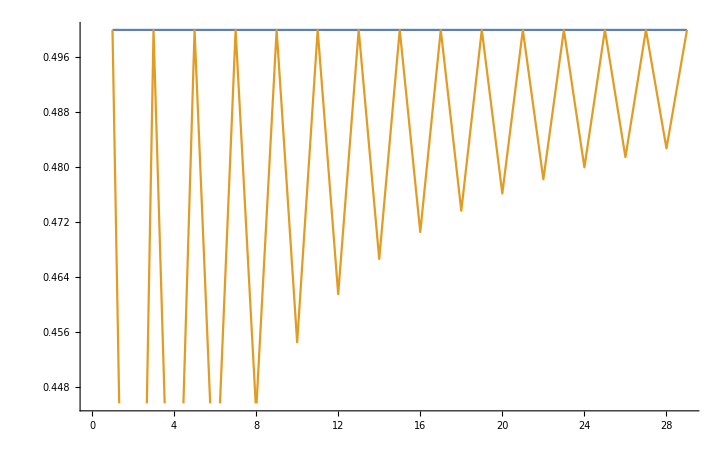

```mathematica
ListPlot[{ConstantArray[1/2,29],N[Table[Ceiling[(m(m-1))/(2(m+1))]/m,{m,2,30}]]},Joined->True]
```

```mathematica
FullSimplify[m+2+(m+m^2)/2-1+∑_(i=2)^(2+e) (m(i-1)+(2-e)i+1)]
```

1/2 (12-e (-8+e (3+e))+5 m+e (3+e) m+m^2)

```mathematica
Expand[%]
```

6+4 e-(3 e^2)/2-e^3/2+(5 m)/2+(3 e m)/2+(e^2 m)/2+m^2/2

```mathematica
Factor[%]
```

1/2 (12+8 e-3 e^2-e^3+5 m+3 e m+e^2 m+m^2)

```mathematica
Reduce[{1/2 (12+8 e-3 e^2-e^3+5 m+3 e m+e^2 m+m^2)==1/2 (12+8 (e+1)-3 (e+1)^2-(e+1)^3+5 m+3 (e+1) m+(e+1)^2 m+m^2),m≥2&&5≤e≤m-2},e,Integers]
```

m==13&&e==8

```mathematica
CoefficientList[%,e]
```

{6+(5 m)/2+m^2/2,4+(3 m)/2,-3/2+m/2,-1/2}

```mathematica
Minimize[1/2 (12-e (-8+e (3+e))+5 m+e (3+e) m+m^2),m≥2&&5≤e≤m-2,e]
```

{Piecewise[{{108, m==7}, {1/2 (-148+45 m+m^2), m≥10}, {1/2 (-8+11 m+3 m^2), 7<m<10}, {∞, True}}],{e→Piecewise[{{5, m==7}, {Indeterminate, !(m==7||m≥10||7<m<10)}, {Root[-160+40 m+(-8-3 m) #1+(3-m) #1^2+#1^3&,2], m≥10}, {Root[-20+6 m+2 m^2+(-8-3 m) #1+(3-m) #1^2+#1^3&,3], True}}]}}

```mathematica
Reduce[{m+2+(m+m^2)/2+am(1-m)+a1(3-e)-1+∑_(i=2)^(2+e-am-a1) (m(i-1)+(2-e)i+1)≤1/2 ((1+m)(2+m)),0≤am≤1,0≤a1≤1,m≥2&&0≤am+a1≤e≤m-2},b,Integers]
```

False

```mathematica
Reduce[{m+2+(m+m^2)/2+am(1-m)+a1(3-e)-1+∑_(i=2)^(2+e-am-a1) (m(i-1)+(2-e)i+1)≤1/2 (4+m+m^2),0≤am≤1,0≤a1≤1,m≥2&&0≤am+a1≤e≤m-2},b,Integers]
```

False

```mathematica
FullSimplify[1/2 ((1+c/n)(2+c/n))]
```

```mathematica
Reduce[{3≤n≤c≤n(n-3)/2,n^(3/2)/(√2)+n≤n-2},Integers]
```

False

```mathematica
"This (below) seems to show that sufficiently large cases might always work, so how large is significantly?";
```

```mathematica
Limit[(Floor[-(3 n)/2+1/2 √(-3 n^2+2 n^3)]-n)/n^(3/2),n->∞]
```

1/(√2)

```mathematica
Reduce[{-(-(3 n)/2+1/2 √(-3 n^2+2 n^3)-n)/n^(3/2)+n^(3/2)/(√2)+n>100,n≥3},Integers]
```

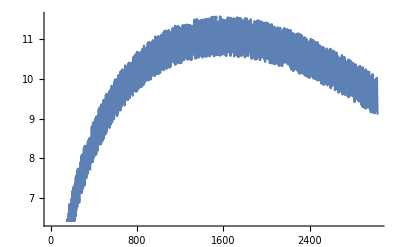

```mathematica
ListPlot[Table[{n,-Floor[-(3 n)/2+1/2 √(-3 n^2+2 n^3)]/(1(*n^(3/2)*))+n^(3/2)/(√2)-√2.27 n},{n,6,3026}],Joined->True]
```

```mathematica
FullSimplify[n/n (4+c/n+(c/n)^2)]
```

4+(c (c+n))/n^2

```mathematica
Reduce[{3≤n≤c≤n(n-3)/2,4+(c (c+n))/n^2≤n-2},Integers]
```

(c|n)∈Integers&&((n==8&&c==8)||(n≥9&&n≤c≤-n/2+1/2 √(-23 n^2+4 n^3)))

```mathematica
1/2 (4+m+m^2)+1/2 (4+(k-m)+(k-m)^2)
1/2( 4+m+m^2+4+(k-m)+(k-m)^2)
1/2( 4+m+m^2+4+k-m+k^2-2 k m+m^2)
1/2( 8+m^2+k+k^2-2 k m+m^2)'
1/2( 4m-2 k)==0
 4m-2 k==0
m==k/2
m==n

m+n==k
k-m==n
```

```mathematica
FullSimplify[(m^2-m^2/2+m/2-e m+m)+i(-m-1/2+e-1)+i^2/2]
```

1/2 (i-m) (-3+2 e+i-m)

```mathematica
Simplify[Reduce[{1/2 (i-m) (-3+2 e+i-m)>1/2 ((i+1)-m) (-3+2 e+(i+1)-m),1≤i≤m-1,0≤e≤m}],1≤i≤m-1&&0≤e≤m]
```

(m==2&&i==1&&e<2)||(m>2&&e+i<1+m)

```mathematica
Simplify[Reduce[{1/2 (i-m) (-3+2 e+i-m)<1/2 ((i+1)-m) (-3+2 e+(i+1)-m),1≤i≤m-1,0≤e≤m}],1≤i≤m-1&&0≤e≤m]
```

m>2&&i>1&&e+i>1+m

```mathematica
Simplify[Reduce[{1/2 (i-m) (-3+2 e+i-m)==1/2 ((i+1)-m) (-3+2 e+(i+1)-m),1≤i≤m-1,0≤e≤m}],1≤i≤m-1&&0≤e≤m]
```

e+i==1+m

```mathematica
Reduce[{ForAll[j,1/2 (i-m) (-3+2 e+i-m)≤1/2 ((j)-m) (-3+2 e+(j)-m)],1≤i≤m-1,1≤j≤m-1,0≤e≤m},Integers]
```

(m==5/2&&i==3/2&&1≤j≤3/2&&e==5/2)||(m>5/2&&3/2≤i≤-1+m&&1≤j≤-1+m&&e==1/2 (3-2 i+2 m))

```mathematica
i≥1+m-e≥1+m-(m-1)==2
```

```mathematica
e≥1-i+m
i≥1+m-i
```

```mathematica
Map[Last,%]
```

{0,0,0,0,0,0,-1,-2,-3,-5,-7,-9,-12,-15,-18,-22,-26,-30,-35}

```mathematica
Reduce[i(m-3)-m+1<0&&m≥2&&2≤i≤m-1,Integers]
```

(i==2&&m==3)||(i==2&&m==4)

```mathematica
∑_(i=2)^(m-1) (m(i-1)+(2-m+1)i)
```

1/2 (-6+m+m^2)

```mathematica
Table[Timing[fsummin[j]],{j,2,20}]
```

{{0.00015,0},{0.000205,0},{0.000446,0},{0.000777,0},{0.001757,0},{0.003713,0},{0.007769,0},{0.016835,0},{0.04134,0},{0.097389,0},{0.212049,0},{0.423331,0},{0.862252,0},{1.76424,0},{3.79444,0},{7.85815,0},{16.0447,0},{33.4639,0},{70.2888,0}}

```mathematica
Column[%]
```

{0.00015,0}
{0.000205,0}
{0.000446,0}
{0.000777,0}
{0.001757,0}
{0.003713,0}
{0.007769,0}
{0.016835,0}
{0.04134,0}
{0.097389,0}
{0.212049,0}
{0.423331,0}
{0.862252,0}
{1.76424,0}
{3.79444,0}
{7.85815,0}
{16.0447,0}
{33.4639,0}
{70.2888,0}

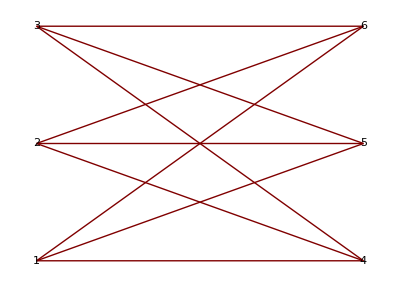

```mathematica
GraphPlot[CompleteGraph[{3,3}],VertexLabeling->True]
```

```mathematica
1,2,3
4,5,6
```

```mathematica
1-2-3-6-5-4-1
```

```mathematica
Table[Mod[i-1,9]+1,{i,1,16}]
```

{1,2,3,4,5,6,7,8,9,1,2,3,4,5,6,7}

```mathematica
edgeloop[l_]:=Block[{len=Length[l]},Table[(Mod[i-1,len]+1)<->(Mod[i,len]+1),{i,1,len}]]
edgeloop[{1,2,3}]
```

{1<->2,2<->3,3<->1}

```mathematica
kpathslist[i_,j_]:=
Block[{elorig=Sort[Map[Sort,EdgeList[CompleteGraph[{i,j}]]]],
cycleindices=Join[Range[1,i],Range[i+1,i+j]]},
Block[{elcycle=Sort[Map[Sort,edgeloop[cycleindices]]]},
Block[{elist=Join[elcycle,elorig]},
Block[{graph=Graph[elist],
n=i+j},
Block[{badedgeposlist=Range[-n,-1]},


Map[SortBy[#,Abs]&,Table[Select[Map[Complement[#,Range[1,n]]&,Select[Map[path2nums[#,Map[{#[[1]],#[[2]]}&,elist]]&,FindPath[graph,Mod[i0-1,n]+1,Mod[i0,n]+1,∞,All]],DisjointQ[badedgeposlist,#]&]],Length[#]>0&],{i0,1,n}],{2}]

]]]]]
```

```mathematica
path2nums[
```

```mathematica
Table[Map[Complement[#,Range[1,n]]&,],{i0,1,n}]
```

```mathematica
k43ps=kpathslist[4,3]
```

{{{9,-12},{8,-11},{-13},{9,-13},{8,-12},{9,-11,-18},{9,-13,-18,19},{9,-11,14,-15},{9,-13,-15,16},{8,-13},{8,-12,-14,15},{8,-13,-14,16},{-12,18,-19},{-11,-19},{-12,15,-16},{-11,14,-16},{9,-11,-15},{9,-13,-15,19},{9,-11,-19},{9,-11,14,-16},{8,-13,-18,19},{8,-13,-15,16},{8,-13,-14,15},{8,-12,-14,18},{8,-13,-14,19},{-12,-19},{-12,14,-16},{-12,-16,18},{-11,-16},{9,-13,-14,16,-18},{9,-11,14,-16,-18,19},{9,-11,-15,16,-19},{9,-11,-16},{8,-13,-15,19},{8,-13,-14,15,-18,19},{8,-13,-14,18},{8,-12,-14,16,18,-19},{-11,14,-15,18,-19},{-12,-14,15,-19},{-11,15,-16,-18},{-12,-16}},{{12,-15},{11,-14},{13,-16},{12,-16},{11,-15},{12,-14,-18},{12,-16,-18,19},{8,-9,12,-14},{-9,12,-16},{11,-16},{-8,9,11,-15},{-8,11,-16},{13,-15,18,-19},{13,-14,-19},{12,-14,-19},{11,-16,-18,19},{-9,11,-16},{-8,9,11,-16},{13,-15,-19},{-8,12,-16,-18},{-9,12,-14,-19},{-8,9,11,-16,-18,19},{-8,11,-15,18,-19},{8,-9,13,-14,18,-19},{-8,9,13,-15,-19}},{{15,-18},{16,-19},{15,-19},{14,-18},{-12,13,15,-19},{-9,15,-19},{14,-19},{-11,12,14,-18},{-11,13,14,-19},{-8,9,14,-18},{-8,14,-19},{12,-13,16,-18},{-9,13,15,-19},{-12,13,14,-19},{-9,14,-19},{-11,12,14,-19},{-8,9,14,-19},{-8,12,14,-18},{-8,13,14,-19},{11,-13,16,-18},{-8,11,-12,15,-19},{8,-9,-11,13,15,-19},{-9,13,14,-19},{-9,-11,12,14,-19},{-8,9,-12,13,14,-19},{-8,12,-13,14,-18},{-8,12,14,-19},{-8,9,11,-13,16,-18}},{{14,-15,18},{11,-12,18},{8,-9,18},{14,-16,19},{11,-13,19},{14,-16,18},{11,-13,18},{-12,14,18},{-9,11,18},{-13,14,19},{11,-13,-15,16,18},{-13,14,18},{-12,13,14,-16,18},{-9,14,-16,18},{-9,11,-13,18},{-9,14,18},{11,-12,15,-16,19},{8,-9,15,-16,19},{12,-13,14,-15,19},{8,-9,12,-13,19},{-9,-13,14,18},{-9,13,14,-16,18},{-9,11,15,-16,19},{8,-9,-13,15,19}},{{-14,15},{-11,12},{-8,9},{-14,18},{-11,15},{-8,12},{-14,16,18,-19},{12,-13,-14,16},{-11,18},{-11,13,18,-19},{-11,13,15,-16},{-8,18,-19},{-8,15,-16},{-8,12,-13},{-8,15},{12,-13,-14,19},{-11,16,18,-19},{-11,13,-16,18},{-8,-16,18},{-8,-13,15},{-8,18},{-8,13,18,-19},{-8,13,15,-16},{-8,-13,18},{-8,16,18,-19},{-8,13,-16,18}},{{-18,19},{-15,16},{-12,13},{-9},{-15,19},{-12,16},{-9,13},{-14,16,-18},{-11,13,-18},{-8,-18},{-11,13,14,-15},{-8,14,-15},{11,-12,-14,16},{-8,11,-12},{-12,19},{8,-9,-14,16},{8,-9,-11,13},{-9,16},{-11,16,-18},{-8,13,-18},{-8,13,14,-15},{-11,13,-15},{-8,-15},{11,-12,-14,19},{-8,-12,14},{8,-9,-14,19},{8,-9,-11,16},{-9,11,-14,16},{-9,19},{-8,16,-18},{-8,13,-15},{-8,-12},{8,-9,-11,19},{-9,11,-14,19}},{{-9,18,-19},{-8,-19},{-9,15,-16},{-8,14,-16},{-9,12,-13},{-8,11,-13},{-9,-19},{-9,14,-16},{-9,-16,18},{-8,-16},{-9,11,-13},{-9,-13,15},{-8,-13,14},{-8,14,-15,18,-19},{-8,11,-12,18,-19},{-9,-14,15,-19},{-9,-11,12,-19},{-8,15,-16,-18},{-8,11,-12,15,-16},{-9,-11,12,14,-16},{-9,-16},{-8,12,-13,-18},{-8,12,-13,14,-15},{-9,11,-13,-14,15},{-9,-13,14},{-9,-13,18},{-8,-13},{-8,-12,14,18,-19},{-9,-11,15,-19},{-8,11,-12,-16,18},{-9,-11,12,-16},{-8,12,-13,-15},{-9,11,-13,-14,18},{-8,-13,15,-18},{-9,-13}}}

```mathematica
Map[Select[#,MemberQ[#,8]||MemberQ[#,-8]&]&,k43ps]//Column
```

{{8,-11},{8,-12},{8,-13},{8,-12,-14,15},{8,-13,-14,16},{8,-13,-18,19},{8,-13,-15,16},{8,-13,-14,15},{8,-12,-14,18},{8,-13,-14,19},{8,-13,-15,19},{8,-13,-14,15,-18,19},{8,-13,-14,18},{8,-12,-14,16,18,-19}}
{{8,-9,12,-14},{-8,9,11,-15},{-8,11,-16},{-8,9,11,-16},{-8,12,-16,-18},{-8,9,11,-16,-18,19},{-8,11,-15,18,-19},{8,-9,13,-14,18,-19},{-8,9,13,-15,-19}}
{{-8,9,14,-18},{-8,14,-19},{-8,9,14,-19},{-8,12,14,-18},{-8,13,14,-19},{-8,11,-12,15,-19},{8,-9,-11,13,15,-19},{-8,9,-12,13,14,-19},{-8,12,-13,14,-18},{-8,12,14,-19},{-8,9,11,-13,16,-18}}
{{8,-9,18},{8,-9,15,-16,19},{8,-9,12,-13,19},{8,-9,-13,15,19}}
{{-8,9},{-8,12},{-8,18,-19},{-8,15,-16},{-8,12,-13},{-8,15},{-8,-16,18},{-8,-13,15},{-8,18},{-8,13,18,-19},{-8,13,15,-16},{-8,-13,18},{-8,16,18,-19},{-8,13,-16,18}}
{{-8,-18},{-8,14,-15},{-8,11,-12},{8,-9,-14,16},{8,-9,-11,13},{-8,13,-18},{-8,13,14,-15},{-8,-15},{-8,-12,14},{8,-9,-14,19},{8,-9,-11,16},{-8,16,-18},{-8,13,-15},{-8,-12},{8,-9,-11,19}}
{{-8,-19},{-8,14,-16},{-8,11,-13},{-8,-16},{-8,-13,14},{-8,14,-15,18,-19},{-8,11,-12,18,-19},{-8,15,-16,-18},{-8,11,-12,15,-16},{-8,12,-13,-18},{-8,12,-13,14,-15},{-8,-13},{-8,-12,14,18,-19},{-8,11,-12,-16,18},{-8,12,-13,-15},{-8,-13,15,-18}}

```mathematica
Sort[DeleteDuplicates[Map[Abs,Flatten[%]]]]
```

{7,8,10,11,12,14,15}

```mathematica
]
```

{{1},{8,-11},{7,-10},{2,-12},{8,-5,-10},{8,-14,-3},{8,6,-12},{7,5,-11},{7,-4,-3},{2,-6,-11},{2,-15,-3},{8,-5,-4,-3},{8,-14,4,-10},{8,-14,15,-12},{8,6,-15,-3},{7,5,-14,-3},{7,5,6,-12},{7,-4,14,-11},{7,-4,15,-12},{2,-6,-5,-10},{2,-6,-14,-3},{2,-15,14,-11},{2,-15,4,-10},{8,-5,-4,15,-12},{8,6,-15,4,-10},{7,5,-14,15,-12},{7,5,6,-15,-3},{7,-4,14,6,-12},{7,-4,15,-6,-11},{2,-6,-5,-4,-3},{2,-6,-14,4,-10},{2,-15,14,-5,-10},{2,-15,4,5,-11}}

```mathematica
Disj
```

```mathematica
Range[-3,-1]
```

{-3,-2,-1}

```mathematica
kpathslist[3,3]
```

{1<->2,1<->4,1<->5,1<->6,1<->6,2<->3,2<->4,2<->5,2<->6,3<->4,3<->4,3<->5,3<->6,4<->5,5<->6}

```mathematica
FindPath[Graph[%],1,2,∞,All]
```

{{1,2},{1,6,2},{1,5,2},{1,4,2},{1,6,3,2},{1,6,5,2},{1,5,3,2},{1,5,6,2},{1,5,4,2},{1,4,3,2},{1,4,5,2},{1,6,3,5,2},{1,6,3,4,2},{1,6,5,3,2},{1,6,5,4,2},{1,5,3,6,2},{1,5,3,4,2},{1,5,6,3,2},{1,5,4,3,2},{1,4,3,6,2},{1,4,3,5,2},{1,4,5,3,2},{1,4,5,6,2},{1,6,3,5,4,2},{1,6,3,4,5,2},{1,6,5,3,4,2},{1,6,5,4,3,2},{1,5,6,3,4,2},{1,5,4,3,6,2},{1,4,3,6,5,2},{1,4,3,5,6,2},{1,4,5,3,6,2},{1,4,5,6,3,2}}

```mathematica
Map[{#[[1]],#[[2]]}&,Out[170]]
```

{{1,2},{1,4},{1,5},{1,6},{1,6},{2,3},{2,4},{2,5},{2,6},{3,4},{3,4},{3,5},{3,6},{4,5},{5,6}}

```mathematica
epos[elist_,e_]:=(Piecewise[{{1, e[[1]]<e[[2]]}, {-1, True}}])*First[First[Position[elist,Sort[e]]]]
```

```mathematica
epos[Out[172],{5,2}]
```

-8

```mathematica
pairs[l_]:=Table[{l[[i]],l[[i+1]]},{i,1,Length[l]-1}]
```

```mathematica
path2nums[path_,elist_]:=Map[epos[elist,#]&,pairs[path]]
```

```mathematica
Map[path2nums[#,Out[172]]&,Out[171]]
```

{{1},{4,-9},{3,-8},{2,-7},{4,-13,-6},{4,-15,-8},{3,-12,-6},{3,15,-9},{3,-14,-7},{2,-10,-6},{2,14,-8},{4,-13,12,-8},{4,-13,10,-7},{4,-15,-12,-6},{4,-15,-14,-7},{3,-12,13,-9},{3,-12,10,-7},{3,15,-13,-6},{3,-14,-10,-6},{2,-10,13,-9},{2,-10,12,-8},{2,14,-12,-6},{2,14,15,-9},{4,-13,12,-14,-7},{4,-13,10,14,-8},{4,-15,-12,10,-7},{4,-15,-14,-10,-6},{3,15,-13,10,-7},{3,-14,-10,13,-9},{2,-10,13,-15,-8},{2,-10,12,15,-9},{2,14,-12,13,-9},{2,14,15,-13,-6}}

```mathematica
Map[epos[Out[172],#]&,pairs[Out[171][[3]]]]
```

{3,-8}

```mathematica
EdgeCount[Graph[kpathslist[3,3]]]
```

15

```mathematica
FindPath[CompleteGraph[4],1,2,∞,All]
```

{{1,2},{1,4,2},{1,3,2},{1,4,3,2},{1,3,4,2}}

```mathematica
FullSimplify[∑_(i=1)^(m-1) (∑_(j=1)^i Subscript[a, j]),m≥2&&Element[m,Integers]]
```

```mathematica
Table[Expand[∑_(i=1)^(-1+m) (∑_(j=1)^i Subscript[a, j])^2],{m,2,8}]//Column
```

a_1^2
2 a_1^2+2 a_1 a_2+a_2^2
3 a_1^2+4 a_1 a_2+2 a_2^2+2 a_1 a_3+2 a_2 a_3+a_3^2
4 a_1^2+6 a_1 a_2+3 a_2^2+4 a_1 a_3+4 a_2 a_3+2 a_3^2+2 a_1 a_4+2 a_2 a_4+2 a_3 a_4+a_4^2
5 a_1^2+8 a_1 a_2+4 a_2^2+6 a_1 a_3+6 a_2 a_3+3 a_3^2+4 a_1 a_4+4 a_2 a_4+4 a_3 a_4+2 a_4^2+2 a_1 a_5+2 a_2 a_5+2 a_3 a_5+2 a_4 a_5+a_5^2
6 a_1^2+10 a_1 a_2+5 a_2^2+8 a_1 a_3+8 a_2 a_3+4 a_3^2+6 a_1 a_4+6 a_2 a_4+6 a_3 a_4+3 a_4^2+4 a_1 a_5+4 a_2 a_5+4 a_3 a_5+4 a_4 a_5+2 a_5^2+2 a_1 a_6+2 a_2 a_6+2 a_3 a_6+2 a_4 a_6+2 a_5 a_6+a_6^2
7 a_1^2+12 a_1 a_2+6 a_2^2+10 a_1 a_3+10 a_2 a_3+5 a_3^2+8 a_1 a_4+8 a_2 a_4+8 a_3 a_4+4 a_4^2+6 a_1 a_5+6 a_2 a_5+6 a_3 a_5+6 a_4 a_5+3 a_5^2+4 a_1 a_6+4 a_2 a_6+4 a_3 a_6+4 a_4 a_6+4 a_5 a_6+2 a_6^2+2 a_1 a_7+2 a_2 a_7+2 a_3 a_7+2 a_4 a_7+2 a_5 a_7+2 a_6 a_7+a_7^2

```mathematica
Table[Expand[(∑_(j=1)^i Subscript[a, j])^2],{i,2,8}]//Column
```

a_1^2+2 a_1 a_2+a_2^2
a_1^2+2 a_1 a_2+a_2^2+2 a_1 a_3+2 a_2 a_3+a_3^2
a_1^2+2 a_1 a_2+a_2^2+2 a_1 a_3+2 a_2 a_3+a_3^2+2 a_1 a_4+2 a_2 a_4+2 a_3 a_4+a_4^2
a_1^2+2 a_1 a_2+a_2^2+2 a_1 a_3+2 a_2 a_3+a_3^2+2 a_1 a_4+2 a_2 a_4+2 a_3 a_4+a_4^2+2 a_1 a_5+2 a_2 a_5+2 a_3 a_5+2 a_4 a_5+a_5^2
a_1^2+2 a_1 a_2+a_2^2+2 a_1 a_3+2 a_2 a_3+a_3^2+2 a_1 a_4+2 a_2 a_4+2 a_3 a_4+a_4^2+2 a_1 a_5+2 a_2 a_5+2 a_3 a_5+2 a_4 a_5+a_5^2+2 a_1 a_6+2 a_2 a_6+2 a_3 a_6+2 a_4 a_6+2 a_5 a_6+a_6^2
a_1^2+2 a_1 a_2+a_2^2+2 a_1 a_3+2 a_2 a_3+a_3^2+2 a_1 a_4+2 a_2 a_4+2 a_3 a_4+a_4^2+2 a_1 a_5+2 a_2 a_5+2 a_3 a_5+2 a_4 a_5+a_5^2+2 a_1 a_6+2 a_2 a_6+2 a_3 a_6+2 a_4 a_6+2 a_5 a_6+a_6^2+2 a_1 a_7+2 a_2 a_7+2 a_3 a_7+2 a_4 a_7+2 a_5 a_7+2 a_6 a_7+a_7^2
a_1^2+2 a_1 a_2+a_2^2+2 a_1 a_3+2 a_2 a_3+a_3^2+2 a_1 a_4+2 a_2 a_4+2 a_3 a_4+a_4^2+2 a_1 a_5+2 a_2 a_5+2 a_3 a_5+2 a_4 a_5+a_5^2+2 a_1 a_6+2 a_2 a_6+2 a_3 a_6+2 a_4 a_6+2 a_5 a_6+a_6^2+2 a_1 a_7+2 a_2 a_7+2 a_3 a_7+2 a_4 a_7+2 a_5 a_7+2 a_6 a_7+a_7^2+2 a_1 a_8+2 a_2 a_8+2 a_3 a_8+2 a_4 a_8+2 a_5 a_8+2 a_6 a_8+2 a_7 a_8+a_8^2

```mathematica
(∑_(j=1)^i Subscript[a, j])^2==∑_(j=1)^i Subscript[a^2, j]+∑_(j≠k)^i Subscript[a, j] Subscript[a, k]
∑_(j=1)^i Subscript[a^2, j]==∑_(j=1)^i Subscript[a, j]
∑_(j≠k)^i Subscript[a, j] Subscript[a, k]==2∑_(j=1)^(i-1) ∑_(k=j+1)^i Subscript[a, j] Subscript[a, k]
```

```mathematica
∑_(i=1)^(m-1) (∑_(j=1)^i Subscript[a, j])^2==∑_(i=1)^(m-1) ∑_(j=1)^i Subscript[a, j]+2∑_(i=1)^(m-1) ∑_(j=1)^(i-1) ∑_(k=j+1)^i Subscript[a, j] Subscript[a, k]
```

```mathematica
Table[∑_(i=1)^(m-1) ∑_(j=1)^(i-1) ∑_(k=j+1)^i Subscript[a, j] Subscript[a, k],{m,2,8}]//Column
```

0
a_1 a_2
2 a_1 a_2+a_1 a_3+a_2 a_3
3 a_1 a_2+2 a_1 a_3+2 a_2 a_3+a_1 a_4+a_2 a_4+a_3 a_4
4 a_1 a_2+3 a_1 a_3+3 a_2 a_3+2 a_1 a_4+2 a_2 a_4+2 a_3 a_4+a_1 a_5+a_2 a_5+a_3 a_5+a_4 a_5
5 a_1 a_2+4 a_1 a_3+4 a_2 a_3+3 a_1 a_4+3 a_2 a_4+3 a_3 a_4+2 a_1 a_5+2 a_2 a_5+2 a_3 a_5+2 a_4 a_5+a_1 a_6+a_2 a_6+a_3 a_6+a_4 a_6+a_5 a_6
6 a_1 a_2+5 a_1 a_3+5 a_2 a_3+4 a_1 a_4+4 a_2 a_4+4 a_3 a_4+3 a_1 a_5+3 a_2 a_5+3 a_3 a_5+3 a_4 a_5+2 a_1 a_6+2 a_2 a_6+2 a_3 a_6+2 a_4 a_6+2 a_5 a_6+a_1 a_7+a_2 a_7+a_3 a_7+a_4 a_7+a_5 a_7+a_6 a_7

```mathematica
m=3,{1,1}
m=4,{2,1},{1,2}
m=5,{3,1},{2,2},{1,3}
m=6,{4,1},{3,2},{2,3},{1,4}
```

```mathematica
"
e trues → e(e-1)/2 pairs of trues.

There are (m-1-k) of size k so
	m-2 of 1
	m-3 of 2
	m-4 of 3
	...
Use pigeonhole principle to make min sum
```

```mathematica
"For now, suppose that all weight 1."
```

```mathematica
Reduce[{m≥2,
0≤e≤m,
q≥0
q/2(2m-q-3)≤e(e-1)≤(q+1)/2(2m-q-1-3),
T≥(e(e-1)/2-q/2(2m-q-3))(q+1)},Integers]
```

(e|m|q|T)∈Integers&&((q==0&&((e==0&&m≥2&&T≥0)||(e==1&&m≥2&&T≥0)||(e≥2&&m≥1/2 (4-2 e+2 e^2)&&T≥1/2 (-e+e^2))))||(q≥1&&((e==0&&m≥(4+5 q+q^2)/(2+2 q)&&T≥1/2 (3 q-2 m q+4 q^2-2 m q^2+q^3))||(e≥1&&m≥(4-2 e+2 e^2+5 q+q^2)/(2+2 q)&&T≥1/2 (-e+e^2+3 q-e q+e^2 q-2 m q+4 q^2-2 m q^2+q^3)))))

```mathematica
Expand[(e(e-1)/2-q/2(2m-q-3))(q+1)]
```

-e/2+e^2/2+(3 q)/2-(e q)/2+(e^2 q)/2-m q+2 q^2-m q^2+q^3/2

```mathematica
LogicalExpand[%]
```

((e|m|q|T)∈Integers&&e==0&&q==0&&m≥2&&T≥0)||((e|m|q|T)∈Integers&&e==0&&m≥(4+5 q+q^2)/(2+2 q)&&q≥1&&T≥1/2 (3 q-2 m q+4 q^2-2 m q^2+q^3))||((e|m|q|T)∈Integers&&e==1&&q==0&&m≥2&&T≥0)||((e|m|q|T)∈Integers&&q==0&&e≥2&&m≥1/2 (4-2 e+2 e^2)&&T≥1/2 (-e+e^2))||((e|m|q|T)∈Integers&&e≥1&&m≥(4-2 e+2 e^2+5 q+q^2)/(2+2 q)&&q≥1&&T≥1/2 (-e+e^2+3 q-e q+e^2 q-2 m q+4 q^2-2 m q^2+q^3))

```mathematica
∑_(k=1)^(q-1) (m-1-k)k
```

-1/6 (-1+q) q (2-3 m+2 q)

```mathematica
FullSimplify[%]
```

-1/6 (-1+q) q (2-3 m+2 q)

```mathematica
∑_(l=1)^q (m-1-l)
```

1/2 (-3 q+2 m q-q^2)

```mathematica
FullSimplify[%]
```

1/2 (-3+2 m-q) q

```mathematica
Reduce[{q/2(2m-q-3)≤p≤(q+1)/2(2m-q-1-3),m≥4,p≥0,q≥0},q,Integers]
```

(m|p|q)∈Integers&&((m==4&&((p==0&&q==0)||(p==1&&q==0)||(p==2&&(q==0||q==1))||(p==3&&(q==1||q==2))))||(m≥5&&((p==0&&q==0)||(0<p≤-2+m&&0≤q≤1/2 (-3+2 m)-1/2 √(9-12 m+4 m^2-8 p))||(-2+m<p<1/2 (2-3 m+m^2)&&1/2 (-5+2 m)-1/2 √(9-12 m+4 m^2-8 p)≤q≤1/2 (-3+2 m)-1/2 √(9-12 m+4 m^2-8 p))||(1/2 (2-3 m+m^2)≤p<1/8 (9-12 m+4 m^2)&&1/2 (-5+2 m)-1/2 √(9-12 m+4 m^2-8 p)≤q≤1/2 (-5+2 m)+1/2 √(9-12 m+4 m^2-8 p)))))

```mathematica
CompleteTheSquare[p_,var_]:=Block[{l=CoefficientList[p,var]},l[[3]](FullSimplify[var+l[[2]]/(2 (l[[3]]))])^2+(FullSimplify[l[[1]]-(l[[2]])^2/(4(l[[3]]))])]
```

```mathematica
CompleteTheSquare[Expand[2(x+3)^2-4],x]
```

-4+2 (3+x)^2

```mathematica
CompleteTheSquare[q m-q^2/2-3/2 q,q]
```

1/8 (3-2 m)^2-1/2 (3/2-m+q)^2

```mathematica
Reduce[b≤a^2,a]
```

a∈Reals&&(b≤0||(b>0&&(a≤-√b||a≥√b)))

```mathematica
Abs[a]≥√b
```

```mathematica
CoefficientList[a x^2+b x+c,x]
```

{c,b,a}

```mathematica
Table[{n,Length[Select[Block[{m=n},DeleteDuplicates[Map[Sort,Flatten[Table[{i,j},{i,1,m},{j,1,m}],1]]]],#[[1]]≠#[[2]]&]]},{n,1,10}]
```

{{1,0},{2,1},{3,3},{4,6},{5,10},{6,15},{7,21},{8,28},{9,36},{10,45}}

```mathematica
InterpolatingPolynomial[%,e]
```

(1+1/2 (-2+e)) (-1+e)

```mathematica
FullSimplify[%]
```

1/2 (-1+e) e

```mathematica
FullSimplify[∑_(j=i)^(m-1) j]
```

```mathematica
1/2 (m-i) (m+i-1)
```

```mathematica
Expand[(m-i) (m+i-1)]
```

i-i^2-m+m^2

```mathematica
m^2-m+i-i^2
```